Posplošeni lotka-volterra

1.01

1.04171

1

1

{{k→InterpolatingFunction[…],z→InterpolatingFunction[…],l→InterpolatingFunction[…]}}

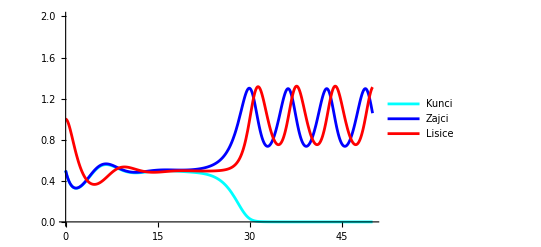

-Graphics-

-Graphics3D-

```mathematica
a=1.01
b=1.041713
c=1
d=1
fz = {k - alk - kz, az - lz -bkz, dlk + adlz - cl};
s=NDSolve[{k'[t]== k[t] - a l [t] k[t] -  k[t]z[t], z'[t]== a z[t] - l[t]z[t] -b k[t]z[t], l'[t] == d l[t]k[t] + a d l[t]z[t] -c l[t],k[0]==0.5, z[0]==0.5, l[0]==1},{k, z, l},{t,0,50}]
Plot[Evaluate[{k[t], z[t], l[t]} /.s], {t, 0,50}, PlotLegends->{"Kunci", "Zajci", "Lisice"}, PlotRange->{{0,50}, {0,2}}, PlotStyle->{Cyan, Blue, Red}]
ParametricPlot[Evaluate[{k[t]+ z[t], l[t]} /.s], {t, 0, 20}, AxesLabel->{"Zajci in kunci", "Lisice"},ColorFunction->Function[{x,y,z},Hue[-z/10 -0.4]]]
StreamPlot3D[fz, {z, 0,3}, {k, 0, 3}, {l,0,3}]
```

preživetje vrst

```mathematica
J={{1-z, -ax, -x}, {0,a-x-bz,0}, {dz, adz, -c+dx}}
Eigenvalues[J]
```

{{1-z,-ax,-x},{0,a-bz-x,0},{dz,adz,-c+dx}}

{a-bz-x,1/2 (1-c+dx-z-√((-1+c-dx+z)^2-4 (-c+dx+dz x+c z-dx z))),1/2 (1-c+dx-z+√((-1+c-dx+z)^2-4 (-c+dx+dz x+c z-dx z)))}

Konkurenčni Lotka-Volterra

1

1.01

1

0.1

0.3

-0.01

{k (1-k-0.3 l-0.1 z),1.01 (1-0.2 k-0.3 l-z) z,l (1+0.01 k-l+0.01 z)}

{{k→InterpolatingFunction[…],z→InterpolatingFunction[…],l→InterpolatingFunction[…]}}

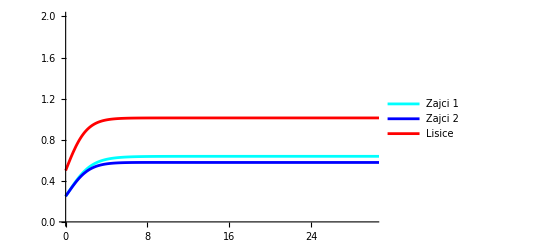

-Graphics-

-Graphics3D-

```mathematica
a=1
b=1.01
c=1
d=0.1
f=0.3
g=-0.01
fz = {a k(1-( k+d z+f l)) , b z(1-( (d + 0.1) k + z+f l)), c l(1-( g k +g z + l))}
s=NDSolve[{k'[t]==   k[t](a-( k[t]+d z[t]+f l[t])) , z'[t]==   z[t](b-((d+0.1) k[t]+ z[t]+f l[t])), l'[t] ==  l[t](c-(g k[t] + g z[t]+ l[t])),k[0]==0.25, z[0]==0.25, l[0]==00.5},{k, z, l},{t,0,50}]
Plot[Evaluate[{k[t], z[t], l[t]} /.s], {t, 0,50}, PlotLegends->{"Zajci 1", "Zajci 2", "Lisice"}, PlotRange->{{0,30}, {0,2}}, PlotStyle->{Cyan, Blue, Red}]
ParametricPlot[Evaluate[{k[t]+ z[t], l[t]} /.s], {t, 0, 20}, AxesLabel->{"Zajci in kunci", "Lisice"},ColorFunction->Function[{x,y,z},Hue[-z/10 -0.4]]]
StreamPlot3D[fz, {z, 0,3}, {k, 0, 3}, {l,0,3}]
```

test

```mathematica
s=NDSolve[{k'[t]==  k[t] - l [t] k[t] - a k[t]z[t], z'[t]== a z[t] - l[t]z[t] -  k[t]z[t], l'[t] == c l[t]k[t] + c a l[t]z[t] -b l[t],k[0]==1, z[0]==1, l[0]==1},{k[t], z[t], l[t]},{t,0,10}][[1]]
Manipulate[Module[dsolution, dsolution = {k[t], z[t], l[t]}/.s; Show[Plot[dsolution, {t, 0, 10}]]], {a,1,2}, {b, 1, 2}, {c, 1, 2}]
```

NDSolve::ndode: The equations {{3/2,-1,-1/2}[0]==1} are not differential equations or initial conditions in the dependent variables {k,z}.

{k'[t]==k[t]-k[t] z[t]-k[t] {3/2,-1,-1/2}[t],z'[t]==z[t]-k[t] z[t]-z[t] {3/2,-1,-1/2}[t],{3/2,-1,-1/2}'[t]==-{3/2,-1,-1/2}[t]+k[t] {3/2,-1,-1/2}[t]+z[t] {3/2,-1,-1/2}[t],k[0]==1,z[0]==1,{3/2,-1,-1/2}[0]==1}

Module::lvlist: Local variable specification dsolution is not a List.

Zajci test

```mathematica
cajt = 70
Manipulate[Module[{dsolution}, dsolution = {k[t], z[t], l[t]}/.NDSolve[{k'[t]== a k[t] - b l [t] k[t] - c k[t]z[t], z'[t]== (a + d) z[t] - b l[t]z[t] - c k[t]z[t], l'[t] == l[t]k[t] + l[t]z[t] - l[t],k[0]==0.5, z[0]==0.5, l[0]==1},{k[t], z[t], l[t]},{t,0,cajt}][[1]]; Plot[dsolution, {t,0,cajt}, PlotLegends->{"Kunci", "Zajci", "Lisice"}, PlotRange->{{0,cajt}, {0,2}}, PlotStyle->{Red, Orange, Blue}]], {{a, 1}, 0.1, 2}, {{b, 1}, 0.1, 2}, {{c, 1}, 0.1, 2}, {{d, 0.01}, 0.01, 0.5}]
```

70

NDSolve::ndode: The equations {{3/2,-1,-1/2}[0]==1} are not differential equations or initial conditions in the dependent variables {k,z}.

ReplaceAll::reps: {k'[t]==k[t]-k[t] z[t]-k[t] {3/2,-1,-1/2}[t],z'[t]==1.01 z[t]-k[t] z[t]-z[t] {3/2,-1,-1/2}[t],{3/2,-1,-1/2}'[t]==-{3/2,-1,-1/2}[t]+k[t] {3/2,-1,-1/2}[t]+z[t] {3/2,-1,-1/2}[t],k[0]==0.5,z[0]==0.5,{3/2,-1,-1/2}[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {k'[0.00143]==k[0.00143]-k[0.00143] z[0.00143]-k[0.00143] {3/2,-1,-1/2}[0.00143],z'[0.00143]==1.01 z[0.00143]-k[0.00143] z[0.00143]-z[0.00143] {3/2,-1,-1/2}[0.00143],{3/2,-1,-1/2}'[0.00143]==-{3/2,-1,-1/2}[0.00143]+k[0.00143] {3/2,-1,-1/2}[0.00143]+z[0.00143] {3/2,-1,-1/2}[0.00143],k[0]==0.5,z[0]==0.5,{3/2,-1,-1/2}[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {k'[0.00143]==k[0.00143]-1. k[0.00143] z[0.00143]-1. k[0.00143] {1.5,-1.,-0.5}[0.00143],z'[0.00143]==1.01 z[0.00143]-1. k[0.00143] z[0.00143]-1. z[0.00143] {1.5,-1.,-0.5}[0.00143],{1.5,-1.,-0.5}'[0.00143]==-1. {1.5,-1.,-0.5}[0.00143]+k[0.00143] {1.5,-1.,-0.5}[0.00143]+z[0.00143] {1.5,-1.,-0.5}[0.00143],k[0.]==0.5,z[0.]==0.5,{1.5,-1.,-0.5}[0.]==1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnl: Endpoint cajt in {t, 0., cajt} is not a real number.

ReplaceAll::reps: 
   {k'[t] == k[t] - k[t] l[t] - k[t] z[t], 
     z'[t] == 1.01 z[t] - k[t] z[t] - l[t] z[t], 
     l'[t] == -l[t] + k[t] l[t] + l[t] z[t], k[0] == 0.5, z[0] == 0.5, 
     l[0] == 1} is neither a list of replacement rules nor a valid dispatch
     table, and so cannot be used for replacing.

Plot::plln: Limiting value cajt in {t, 0, cajt}
     is not a machine-sized real number.

NDSolve::ndnl: Endpoint cajt in {t, 0., cajt} is not a real number.

ReplaceAll::reps: 
   {k'[t] == k[t] - k[t] l[t] - k[t] z[t], 
     z'[t] == 1.01 z[t] - k[t] z[t] - l[t] z[t], 
     l'[t] == -l[t] + k[t] l[t] + l[t] z[t], k[0] == 0.5, z[0] == 0.5, 
     l[0] == 1} is neither a list of replacement rules nor a valid dispatch
     table, and so cannot be used for replacing.

Plot::plln: Limiting value cajt in {t, 0, cajt}
     is not a machine-sized real number.

NDSolve::ndnl: Endpoint cajt in {t,0.,cajt} is not a real number.

ReplaceAll::reps: {k'[t]==k[t]-k[t] l[t]-k[t] z[t],z'[t]==1.01 z[t]-k[t] z[t]-l[t] z[t],l'[t]==-l[t]+k[t] l[t]+l[t] z[t],k[0]==0.5,z[0]==0.5,l[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value cajt in {t,0,cajt} is not a machine-sized real number.

NDSolve::ndnl: Endpoint cajt in {t,0.,cajt} is not a real number.

ReplaceAll::reps: {k'[t]==k[t]-k[t] l[t]-k[t] z[t],z'[t]==1.01 z[t]-k[t] z[t]-l[t] z[t],l'[t]==-l[t]+k[t] l[t]+l[t] z[t],k[0]==0.5,z[0]==0.5,l[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value cajt in {t,0,cajt} is not a machine-sized real number.

NDSolve::ndnl: Endpoint cajt in {t, 0., cajt} is not a real number.

ReplaceAll::reps: 
   {k'[t] == k[t] - k[t] l[t] - k[t] z[t], 
     z'[t] == 1.01 z[t] - k[t] z[t] - l[t] z[t], 
     l'[t] == -l[t] + k[t] l[t] + l[t] z[t], k[0] == 0.5, z[0] == 0.5, 
     l[0] == 1} is neither a list of replacement rules nor a valid dispatch
     table, and so cannot be used for replacing.

Plot::plln: Limiting value cajt in {t, 0, cajt}
     is not a machine-sized real number.

Zajci čopar

```mathematica
fzajci={α Z- L Z,- L+ L Z};
Manipulate[Module[{tempfunction,dsolution},tempfunction:=fzajci/.{α->aaa};
dsolution={z[t],l[t]}/.NDSolve[{z'[t]==aaa z[t]- l[t]z[t],l'[t]==- l[t]+ l[t]z[t],z[0]==1,l[0]==0.7},{z[t],l[t]},{t,0,20}][[1]];
{Show[StreamPlot[tempfunction,{Z,0,4},{L,0,4},FrameLabel->{"Plen","Plenilec"}, LabelStyle->{FontSize->18},ImageSize->Large, StreamColorFunction->None]],Plot[dsolution,{t,0,20},PlotLegends->{"Plen","Plenilec"},ImageSize->Medium,PlotRange->{{0,20},{0,2}}]}],{{aaa,1},0.01,5}]
```

```mathematica
fzajci={x-a x y-x z, a y-x y-y z, b z+c x z+c a y z};
Manipulate[Module[tempfunction, tempfunction := fzajci/.{a->aaa, b->bbb, c->ccc}; {Show[StreamPlot3D[tempfunction, {x, 0, 3}, {y, 0, 3}, {z, 0, 3}]]}], {{aaa, 1}0.1, 5}; {{bbb, 1}, 0.1, 3}; {{ccc, 1}, 0.1,3}]
```

Manipulate::vsform: Manipulate argument {{aaa,1} 0.1,5};{{bbb,1},0.1,3};{{ccc,1},0.1,3} does not have the correct form for a variable specification.

Manipulate[Module[tempfunction,tempfunction:=fzajci/.{a→aaa,b→bbb,c→ccc};{Show[StreamPlot3D[tempfunction,{x,0,3},{y,0,3},{z,0,3}]]}],{{aaa,1} 0.1,5};{{bbb,1},0.1,3};{{ccc,1},0.1,3}]